```mathematica
(*Styling of the text*)
st[text_]:=Style[text,Directive[15,FontFamily->"Linux Libertine"]];
```

# Inclined slope

```mathematica
(* approximant size *)
n=5;
```

```mathematica
(* Z^2 lattice *)
θ=-ArcTan[Fibonacci[n]/Fibonacci[n+1]];
θ=ArcTan[1/GoldenRatio];
Δ=2;
z2=Flatten[Table[{x,y},{x,-Δ,Fibonacci[n+1]-1+Δ},{y,-Δ,Fibonacci[n]-1+Δ}],1];
square[{x_,y_}]:=Rectangle[{x,y},{x+1,y+1}];
```

```mathematica
(* projection axis *)
cut=Line[{{0,0},1.2Fibonacci[n+1]{Cos[θ ],Sin[θ]}}];
(* upper limit of the selection region *)
window=Translate[cut,{-1,1}];
```

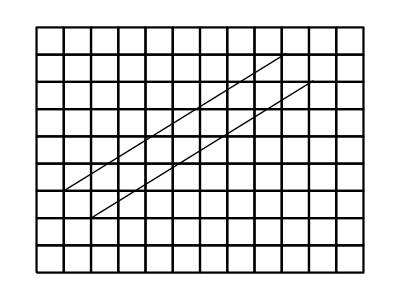

```mathematica
Graphics[{cut,window,{EdgeForm[{Thickness[0.004],Opacity[1.]}],Opacity[0],square/@z2}}]
```

```mathematica
(* enumerate the coordinates of the selected points *)
r[i_]:={Floor[i Fibonacci[n+1]/Fibonacci[n+2]],Ceiling[i Fibonacci[n]/Fibonacci[n+2]]};
```

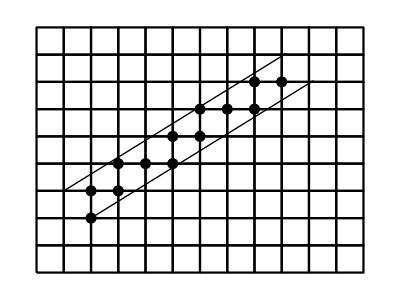

```mathematica
selPts=r/@Range[0,Fibonacci[n+2]-1];
Graphics[{{PointSize[0.02],Point[selPts]},cut,window,{EdgeForm[{Thickness[0.004],Opacity[1]}],Opacity[0],square/@z2}}]
```

```mathematica
c=Fibonacci[n+1]/√(Fibonacci[n]^2+Fibonacci[n+1]^2);
c=Cos[θ];
s=Fibonacci[n]/√(Fibonacci[n]^2+Fibonacci[n+1]^2);
s=Sin[θ];
(* projection of a selected point on the cut axis *)
proj[{x_,y_}]:={c,s}(x c + y s);
(* projection of a selected point on the window *)
orthProj[r_]:=r-proj[r];
```

```mathematica
(* project selected points into the parallel space *)
projPts=proj/@selPts;
(* project selected points into the perp space *)
orthPts=orthProj/@selPts;
(* lines from pts to parallel proj *)
projLines=MapThread[Line[{#1,#2}]&,{selPts,projPts}];
(* lines from pts to perp proj *)
orthLines=MapThread[Line[{#1,#2}]&,{selPts,orthPts}];
```

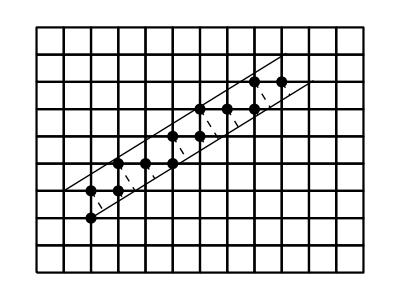

```mathematica
Graphics[{{Dashed,projLines},{PointSize[0.02],Point[selPts]},cut,window,{EdgeForm[{Thickness[0.004],Opacity[1]}],Opacity[0],square/@z2}}]
```

```mathematica
(* on the cut, alternate two types of lines *)
BostonBlue=RGBColor["#00688B"];
comp=RGBColor["#8B2300"];
col1=comp;
col2=BostonBlue;
(* draw a line bewteen points i and i+1 along the cut *)
(* (rf-ri)[[1]] is either 0 (short) or 1 (long) *)
th=0.004;
(*cutLine[i_]:=Block[{ri=r[i],rf=r[i+1]},{Blend[{col1,col2},(rf-ri)[[1]]],{Thickness[th],Line[{proj[ri],proj[rf]}]}}]*)

(* draw a double line for strong bonds, a single line for weak bonds *) 
(* draw a double line *)
DoubleLine[coords_,spacing_]:=Block[{Δv=coords[[2]]-coords[[1]],norm},
Δv=Δv/Norm[Δv];
(* vector normal to the direction of the line *)
norm={-Δv[[2]],Δv[[1]]};
Line[Map[Function[y,coords+y{norm,norm}],{-spacing/2,spacing/2}]]
]
spac=0.1;
cutLine[i_]:=Block[{ri=r[i],rf=r[i+1]},{Thickness[th],If[(rf-ri)[[1]]==1,Line[{proj[ri],proj[rf]}],DoubleLine[{proj[ri],proj[rf]},spac]]}]

(* color projected point in red for atoms, in blue for molecules *)
coloredPt[i_]:=Block[{ri=r[i-1],rf=r[i+1]},{If[(rf-ri)[[1]]==2,BostonBlue,comp],Point[selPts[[i+1]]]}]

(* rotation matrix *)
rot=RotationMatrix[θ];
(* windows width *)
W=Sin[θ]+Cos[θ];
(* spacing in perp space *)
δW=W/Fibonacci[n+2];
(* atomic surface *)
wind=Line[{{0,0},{0,W}}];
(* atoms *)
windAt={BostonBlue,Thickness[th],Line[{rot.{0,(Fibonacci[n]-1/2)δW},rot.{0,(Fibonacci[n+1]-1/2)δW}}]};
(* molecules *)
windMol={comp,Thickness[th],Line[{{0,0},rot.{0,(Fibonacci[n]-1/2)δW}}],Line[{rot.{0,(Fibonacci[n+1]-1/2)δW},rot.{0,W-δW}}]};
```

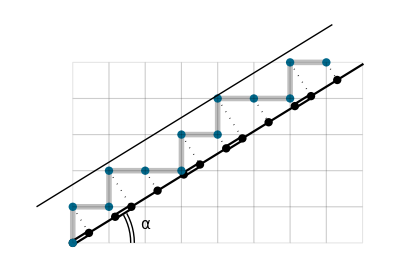

```mathematica
(* same thing, but with focus on parallel space *)
z2p=Flatten[Table[{x,y},{x,0,Fibonacci[n+1]-1},{y,0,Fibonacci[n]-1}],1];
(* project selected points into the parallel space *)
projPts=proj/@selPts;
(* lines from pts to parallel proj *)
projLines=MapThread[Line[{#1,#2}]&,{selPts,projPts}];
(* text *)
δ=0.3;
abs=Text[st@"F_n",{Fibonacci[n+1]/2,-δ-0.1}];
ord=Text[st@"F_(n - 1)",{Fibonacci[n+1]+δ+0.5,Fibonacci[n]/2}];
(* projection angle *)
ang={Text[st@"α",{2.,0.5}],Circle[{0,0},#,{0,0.9 ArcTan[Fibonacci[n]/Fibonacci[n+1]]}]&/@{1.6,1.7}};
(* couplings *)
tts=Text[st@"t_s",{4.55,2.5}];
ttw=Text[st@"t_w",{4.05,2.15}];

Graphics[{ang,{Directive[Gray,Opacity[0.5],Thickness[0.01]],Line[selPts]},{cutLine/@Range[0,Fibonacci[n+2]-1],{Dotted,projLines},{PointSize[0.015],Point[projPts],{BostonBlue,Point[selPts[[#+1]]]}&/@Range[0,Fibonacci[n+2]-1]},window,{EdgeForm[Directive[Opacity[1],Opacity[0.1]]],Opacity[0],square/@z2p}}}]
```

```mathematica
Export[NotebookDirectory[]<>"cut_and_project.pdf",%]
```

/home/nicolas/git/talks/ICQ13 September 2016/talk/img/cut_and_project.pdf

```mathematica
co[i_]:=Mod[Fibonacci[n+1]i,Fibonacci[n+2]];
```

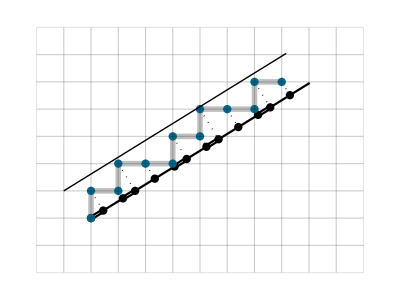

```mathematica
(* atomic surface *)
surf={BostonBlue,Thickness[th],Line[{{0,0},rot.{0,W}}]};
graph=Graphics[{{Directive[Gray,Opacity[0.5],Thickness[0.01]],Line[selPts]},{cutLine/@Range[0,Fibonacci[n+2]-1],{Dotted,projLines},{PointSize[0.015],Point[projPts],{BostonBlue,Point[selPts[[#+1]]]}&/@Range[0,Fibonacci[n+2]-1]},window,{EdgeForm[Directive[Opacity[1],Opacity[0.1]]],Opacity[0],square/@z2}}}]
```

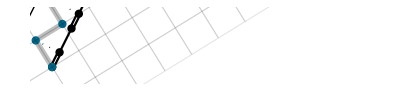

```mathematica
orig={0,0};
δ=0.5;
v=.5;
(* text displacement *)
txtδ=-.15;
(* font size *)
ftsiz=5;
(* conumbering *)
style[string_]:=Style[string,Directive[FontSize->ftsiz,FontFamily->"Linux Libertine"]]
conum=Table[Text[style[i],{txtδ,δW i}],{i,0,Fibonacci[n+2]-1}];
(* numbering in parallel space *)
rotinv=RotationMatrix[θ]; (* rotation from tilted to non tilted *)
pts=Dot[rotinv,#]&/@projPts; (* coords of the points in parallel space, non tilted *)
num=Table[Text[style[co[i]],pts[[i+1]]+{0,txtδ}],{i,0,Fibonacci[n+2]-1}]; 
Graphics[{Rotate[graph,θ,orig]/.Graphics->Identity},PlotRange->{{-δ,√(Fibonacci[n]^2+Fibonacci[n+1]^2)+δ},{-v,W+v}}]
```

```mathematica
Export[NotebookDirectory[]<>"cut_and_project_rotated.pdf",%]
```

/home/nicolas/git/talks/ICQ13 September 2016/talk/img/cut_and_project_rotated.pdf

```mathematica
(* inserting brackets to mark atomic and molecular sites in perp space *)
(* NOTE: the code is extremely ugly: everything is done by hand... *)
curve=First[First[ImportString[ExportString[Style["{",FontFamily->"Linux Libertine",FontSize->12],"PDF"],"TextMode"->"Outlines"]]];
cg=Graphics[curve];
```

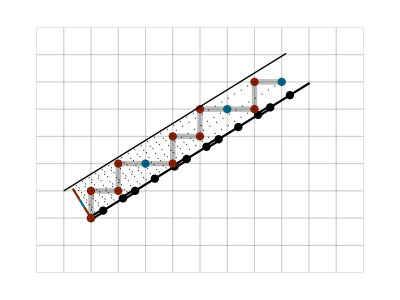

```mathematica
graph=Graphics[{{Directive[Gray,Opacity[0.5],Thickness[0.01]],Line[selPts]},{cutLine/@Range[0,Fibonacci[n+2]-1],{Dotted,orthLines},windMol,windAt,{PointSize[0.015],Point[projPts],coloredPt/@Range[0,Fibonacci[n+2]-1]},window,{EdgeForm[Directive[Opacity[1],Opacity[0.1]]],Opacity[0],square/@z2}}}]
```

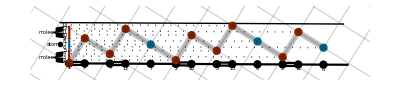

```mathematica
θ=-ArcTan[Fibonacci[n]/Fibonacci[n+1]];
orig={0,0};
δ=0.5;
v=0.5;
(* text displacement *)
txtδ=-.15;
(* font size *)
ftsiz=5;
(* conumbering *)
style[string_]:=Style[string,Directive[FontSize->ftsiz,FontFamily->"Linux Libertine"]]
conum=Table[Text[style[i+1],{txtδ,δW i}],{i,0,Fibonacci[n+2]-1}];
(* numbering in parallel space *)
rotinv=RotationMatrix[θ]; (* rotation from tilted to non tilted *)
pts=Dot[rotinv,#]&/@projPts; (* coords of the points in parallel space, non tilted *)
num=Table[Text[style[co[i]+1],pts[[i+1]]+{0,txtδ}],{i,0,Fibonacci[n+2]-1}]; 
Graphics[{Rotate[graph,θ,orig]/.Graphics->Identity,conum,num,Inset[Pane[cg,ImageSizeAction->"ResizeToFit"],{2txtδ,1.05},{0,0},{1,0.5}],Inset[Pane[cg,ImageSizeAction->"ResizeToFit"],{2txtδ,0.205},{0,0},{1,0.5}],Inset[Pane[cg,ImageSizeAction->"ResizeToFit"],{2txtδ,0.66},{0,0},{1,0.3}],Text[style["atoms"],{2 txtδ-0.2,W/2-δW/2}],Text[style["molecules"],{2 txtδ-0.3,(Fibonacci[n-1]+1) δW/2}],Text[style["molecules"],{2 txtδ-0.3,Fibonacci[n+1]δW+(Fibonacci[n-1]+1) δW/2}]},PlotRange->{{-2.2δ,√(Fibonacci[n]^2+Fibonacci[n+1]^2)+δ},{-v,W+v}}]
```

```mathematica
Export[NotebookDirectory[]<>"cut_and_project_perp_projections.pdf",%]
```

/home/nicolas/git/talks/ICQ13 September 2016/talk/img/cut_and_project_perp_projections.pdf